```mathematica
ClearAll["Global`*"]
Subscript[σ, 11]= ({{1, 0, 0}, {0, 0, 0}, {0, 0, 0}});Subscript[σ, 12]= ({{0, 1, 0}, {0, 0, 0}, {0, 0, 0}});Subscript[σ, 13]= ({{0, 0, 1}, {0, 0, 0}, {0, 0, 0}});Subscript[σ, 21]= ({{0, 0, 0}, {1, 0, 0}, {0, 0, 0}});Subscript[σ, 22]= ({{0, 0, 0}, {0, 1, 0}, {0, 0, 0}});Subscript[σ, 23]= ({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}}); Subscript[σ, 31]= ({{0, 0, 0}, {0, 0, 0}, {1, 0, 0}});Subscript[σ, 32]= ({{0, 0, 0}, {0, 0, 0}, {0, 1, 0}});Subscript[σ, 33]= ({{0, 0, 0}, {0, 0, 0}, {0, 0, 1}});
```

#### Applying the rotating wave approximation 1) The system consits of a three level atom at fixed energies. 2) We consider capacitive coupling with an RF line The various external fields are going to be carried by incident waves: V_field(x,t) = V_field* exp[ik_field x-ω_field t], where I_field is the amplitude of the field ω_field is the frequency of the radiation The atom is being driven by two fields: V_32= |V_32| exp[ik_32 x-ω_32 t] driving the 2→3 transition. VNA V_31=|V_31| exp[ik_31 x-ω_31 t] driving the 1→3 transition Signal generator 3) We break up the Hamiltonian into two convenient Hamiltonians H = H_1+H_2, where H_1 is the Hamiltonian due to the driving field with a small detuning and H_2is the additional term which we treat in the Rotating Wave approximation for a better Hamiltonian 4) We transfer to the rotating frame, where H_int=U^† (H_1+H_2) U+iℏ(∂U^†)/(∂t)U =U^† H_1 U+U^† H_2 U +iℏU^†(iH_1/ℏ)U^†= =U^† H_2 U 5) Apply the RWA to cancel out the fast oscillating terms.

```mathematica
(* 1) The raw atom 2) The RF field*)
Subscript[H, atom]=({{Subscript[Ε, 1], 0, 0}, {0, Subscript[Ε, 2], 0}, {0, 0, Subscript[Ε, 3]}});(Subscript[H, atom]=Subscript[H, atom]/.Subscript[Ε, 1]->Subscript[Ε, 3]-ℏ Subscript[ω, 31]/.Subscript[Ε, 2]->Subscript[Ε, 3]-ℏ Subscript[ω, 32]/.Subscript[ω, 31]->Subscript[ωd, 31]-Subscript[δω, 31]/.Subscript[ω, 32]->Subscript[ωd, 32]-Subscript[δω, 32])//MatrixForm;
(Subscript[H, drive]= ({{0, 0, -ℏ Subscript[Ω, 31] Cos[Subscript[ωd, 31] t]}, {0, 0, -ℏ Subscript[Ω, 32] Cos[Subscript[ωd, 32] t]}, {-ℏ Subscript[Ω, 31] Cos[Subscript[ωd, 31] t], -ℏ Subscript[Ω, 32] Cos[Subscript[ωd, 32] t], 0}})//TrigToExp)//MatrixForm;
(* 3) Split up into two parts*)
(Subscript[H, 1]=({{Subscript[Ε, 3]-ℏ Subscript[ωd, 31], 0, 0}, {0, Subscript[Ε, 3]-ℏ Subscript[ωd, 32], 0}, {0, 0, Subscript[Ε, 3]}}))//MatrixForm;
(Subscript[H, 2]=({{ℏ Subscript[δω, 31], 0, -1/2 ⅇ^(-ⅈ t Subscript[ωd, 31]) ℏ Subscript[Ω, 31]-1/2 ⅇ^(ⅈ t Subscript[ωd, 31]) ℏ Subscript[Ω, 31]}, {0, ℏ Subscript[δω, 32], -1/2 ⅇ^(-ⅈ t Subscript[ωd, 32]) ℏ Subscript[Ω, 32]-1/2 ⅇ^(ⅈ t Subscript[ωd, 32]) ℏ Subscript[Ω, 32]}, {-1/2 ⅇ^(-ⅈ t Subscript[ωd, 31]) ℏ Subscript[Ω, 31]-1/2 ⅇ^(ⅈ t Subscript[ωd, 31]) ℏ Subscript[Ω, 31], -1/2 ⅇ^(-ⅈ t Subscript[ωd, 32]) ℏ Subscript[Ω, 32]-1/2 ⅇ^(ⅈ t Subscript[ωd, 32]) ℏ Subscript[Ω, 32], 0}}))//MatrixForm;
(*Proof that the two expressions are the same*)
Simplify[(Subscript[H, atom]+Subscript[H, drive])-(Subscript[H, 1]+Subscript[H, 2])]//MatrixForm

(*4) Apply the rotating wave transformation, by transforming the Total Hamiltonian with a unitary operation*)
(U= MatrixExp[-I Subscript[H, 1] t/ℏ]);
(Subscript[H, rotatingWave]=ExpandAll[Inverse[U].(Subscript[H, 1]+Subscript[H, 2]).U+I ℏ D[Inverse[U],t].U])//MatrixForm  

(* 5) Then its a case of applying the rotating wave approximation, where we remove the fast oscillating terms e^i2ωt. The basis for this, is that the fast osciallting terms do not coserve energy and in fact average out. See the RWA online for additional information*)
(Subscript[H, rotatingWave]=Simplify[Factor[Subscript[H, rotatingWave]/.(Exp[ExpandAll[a_ Subscript[ωd, 32]]]->0)/.(Exp[ExpandAll[a_ Subscript[ωd, 31]]]->0)]])//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

(ℏ δω_31 | 0 | -(ℏ Ω_31)/2-1/2 ⅇ^(-2 ⅈ t ωd_31) ℏ Ω_31
0 | ℏ δω_32 | -(ℏ Ω_32)/2-1/2 ⅇ^(-2 ⅈ t ωd_32) ℏ Ω_32
-(ℏ Ω_31)/2-1/2 ⅇ^(2 ⅈ t ωd_31) ℏ Ω_31 | -(ℏ Ω_32)/2-1/2 ⅇ^(2 ⅈ t ωd_32) ℏ Ω_32 | 0)

(ℏ δω_31 | 0 | -(ℏ Ω_31)/2
0 | ℏ δω_32 | -(ℏ Ω_32)/2
-(ℏ Ω_31)/2 | -(ℏ Ω_32)/2 | 0)

#### Now we solve the Master Equation 1) So ultimately after the rotating wave approximation, we have the simplified Hamiltonian, which we write H_full=H_a+H_int, redefining some symbols with H_a=ℏ(δω_31 σ_11+δω_32 σ_22) H_int= -ℏ/2[Ω_31(σ_31+σ_13)+Ω_32(σ_23+σ_32)] 2) Now we proceed to solve the master equation, to get the density state matrix ρ of the system. For this we introduce the Linbland term. ℒ = (Γ21 ρ22 | γ12 ρ12 | γ13 ρ13 γ12 ρ21 | -Γ21 ρ22+Γ32 ρ33 | γ23 ρ23 γ13 ρ31 | γ23 ρ32 | -Γ32 ρ33) Γ denote the relaxations between certain levels (e.g. 3-1, 2-1 3-2), while γ is the damping rate of the off diagonal elements, characterising dephasing. There are no thermal excitations, so no excitation terms 3) The atomic dynamics are then goverened by the master equation, which is solved for the stationary state. dρ/dt= -i/ℏ(Hρ-ρH^†)+ℒ[ρ] All this is done for the case where we assume no pure dephasing i.e. γ23 =(Γ32+Γ31+Γ21)/2 etc...

```mathematica
(* 1) Rotating wave approximation already performed, but here for different driving*)
(Subscript[H, full]=({{ℏ Subscript[δω, 32], -(ℏ Subscript[Ω, 21])/2, 0}, {-(ℏ Subscript[Ω, 21])/2, ℏ Subscript[δω, 21], -(ℏ Subscript[Ω, 32])/2}, {0, -(ℏ Subscript[Ω, 32])/2, 0}}))//MatrixForm

(* 2) The Linbland term for interaction with the environment. We assume no pure dephasing - off diagnoal terms in ℒ due to relaxation processes only*)
Γ21=20;Γ32=38;Γ31=41;
γ23 =(Γ32+Γ31+Γ21)/2;γ12 =Γ21/2;γ13 =(Γ32+Γ31)/2;
ρ=({{1-ρ22-ρ33, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}});ℒ=({{Γ21 ρ22+Γ31 ρ33, -γ12 ρ12, -γ13 ρ13}, {-γ12 ρ21, -Γ21 ρ22+Γ32 ρ33, -γ23 ρ23}, {-γ13 ρ31, -γ23 ρ32, -(Γ32 +Γ31) ρ33}}) ;


(* 3) The Master equation of the system, simplfied with real coefficients, which we solve for the stationary state*)
(ρDot=Assuming[{ ℏ,Subscript[δω, 21],Subscript[δω, 32],Subscript[Ω, 21],Subscript[Ω, 32]}∈ Reals,Simplify[(-I/ℏ  Subscript[H, full].ρ+I/ℏ ρ.Subscript[H, full]+ℒ)]])//MatrixForm;
solution  = Solve[(ρDot==0),{ρ33,ρ12,ρ13,ρ21,ρ22,ρ23,ρ31,ρ32}];

(* Prepare for plotting the 1-2 transition*)
t21 = I Γ21 ρ21/.solution[[1]];
```

(ℏ δω_32 | -(ℏ Ω_21)/2 | 0
-(ℏ Ω_21)/2 | ℏ δω_21 | -(ℏ Ω_32)/2
0 | -(ℏ Ω_32)/2 | 0)

```mathematica
splitting[Ω32_,limit_]:=
(
toPlot = Simplify[ComplexExpand[Abs[t21/.Subscript[δω, 31]->0/.Subscript[Ω, 32]->1]]];

DensityPlot[toPlot,{Subscript[Ω, 32],1,10},{Subscript[δω, 32],0,10},PlotPoints->20,
PlotLabel->Style[Row@{"Ω_32=",Ω32,", δω_31=0"," MHz"},FontSize->30],
LabelStyle->{FontSize->20},
ColorFunction->"Ocean",
Frame->True,FrameLabel->{"Ω_31 (MHz)","δω_32/2π (MHz)"},
PlotRange->{Automatic,Automatic,{0,limit}},
(*Epilog->{Text[Style[Row@{"Ω_21=",Ω21,", Ω_31=",Ω31," MHz"},FontSize->30,FontColor->Red],{0,180}],FontSize->20},*)
(*Frame->{{True,True},{True,True}},FrameTicks->{{None,None},{None,None}},
FrameStyle->Directive[Thick,Red],
*)(*PlotRangePadding->None,ImagePadding->None,*)
PlotLegends->BarLegend[{Automatic,{0,limit}},LegendLabel->Style["e",FontSize->20],LabelStyle->{FontSize->20}]
]
)
```

```mathematica
splitting[10,10]
```

```mathematica
density21[Ω32_,Ω21_,limit_,title_]:=
((*PLOT SIMULATION FOR A GIVEN SET OF DRIVING POWERS*)

(*1) Prepare data to plot*)
toPlot = Simplify[ComplexExpand[Abs[t21/.Subscript[Ω, 32]->Ω32/.Subscript[Ω, 21]->Ω21]]];

(*2) Perform plotting of the data*)
(*Manipulate[*)
DensityPlot[toPlot,{Subscript[δω, 32],-200,200},{Subscript[δω, 21],-200,200},PlotPoints->20,
PlotLabel->Style[Row@{title},FontSize->30],
LabelStyle->{FontSize->20},
ColorFunction->"Ocean",
Frame->True,FrameLabel->{"δω_32/2π (MHz)","δω_21/2π (MHz)"},
(*The color function bar manipulation, which prevents overload*)
PlotRange->{Automatic,Automatic,{0,limit}},
(*Epilog->{Text[Style[Row@{"Ω_21=",Ω21,", Ω_31=",Ω31," MHz"},FontSize->30,FontColor->Red],{0,180}],FontSize->20},*)
(*Frame->{{True,True},{True,True}},FrameTicks->{{None,None},{None,None}},
FrameStyle->Directive[Thick,Red],
*)(*PlotRangePadding->None,ImagePadding->None,*)
PlotLegends->BarLegend[{Automatic,{0,limit}},LegendLabel->Style["e",FontSize->20],LabelStyle->{FontSize->20}]
]
(*ColorFunctionScaling->False,
ColorFunction->(ColorData["Ocean"][Rescale[#,{-limit,limit}]]&),
PlotPoints->30],
{limit,0.1,100}
]*)
)
```

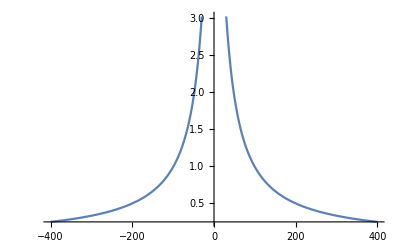

```mathematica
toPlot = Simplify[ComplexExpand[Abs[t21/.Subscript[Ω, 32]->10/.Subscript[Ω, 21]->10/.Subscript[δω, 21]->0]]];
Plot[toPlot, {Subscript[δω, 32],-400,400}]
```

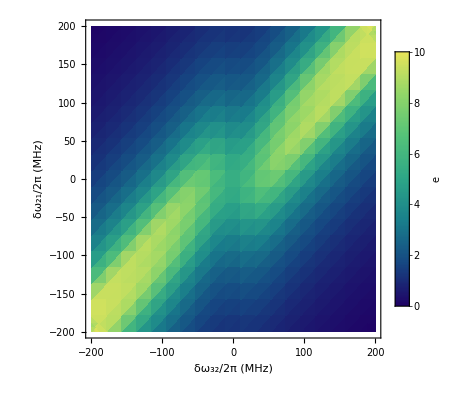

```mathematica
density21[90,30,10,""]
```

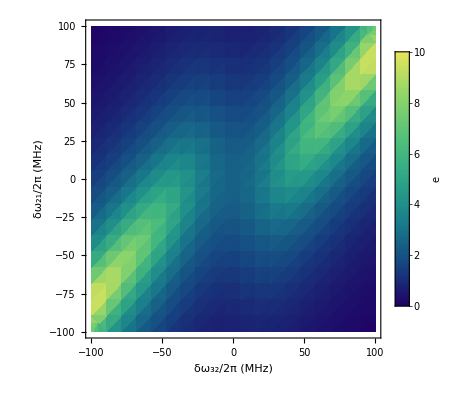

```mathematica
density21[90,10,10,""]
```

```mathematica
|
```

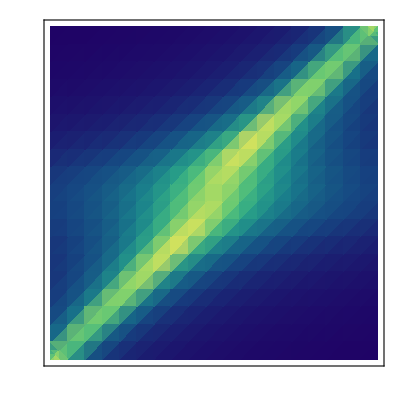

```mathematica
density21[80,20,10]
```

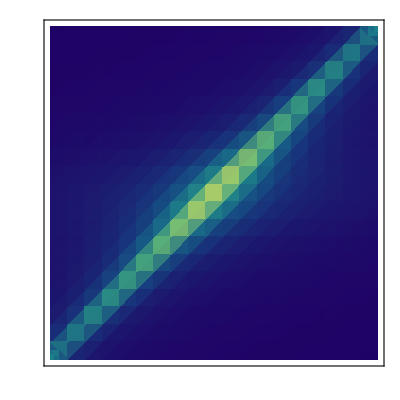

```mathematica
density21[20,20,10]
```

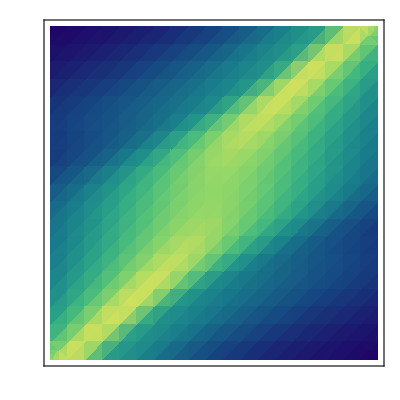

```mathematica
density21[200,70,10]
```

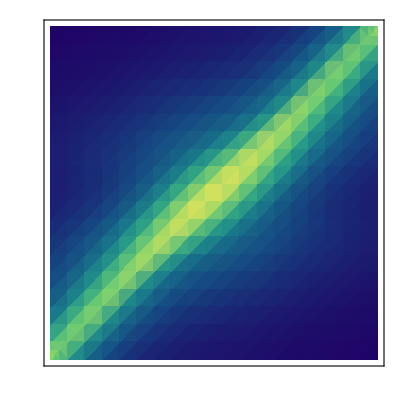

```mathematica
density21[80,70,10]
```

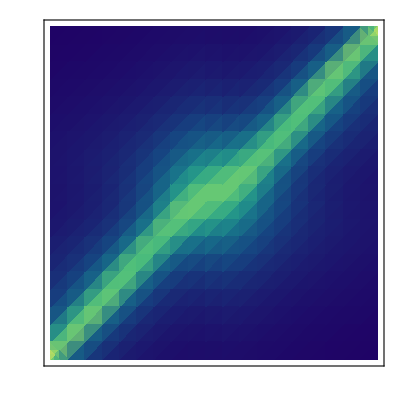

```mathematica
density21[20,70,10]
```

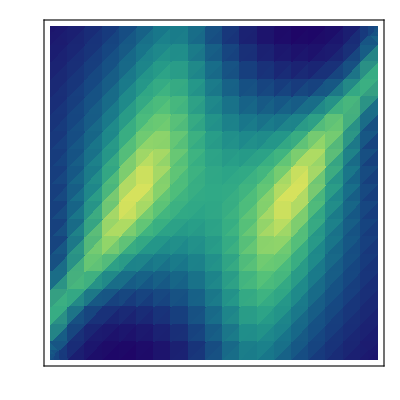

```mathematica
density21[20,210,10]
```

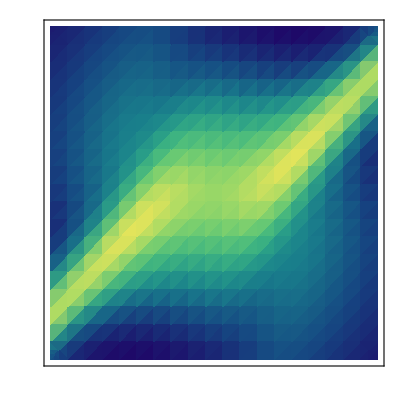

```mathematica
density21[70,210,10]
```

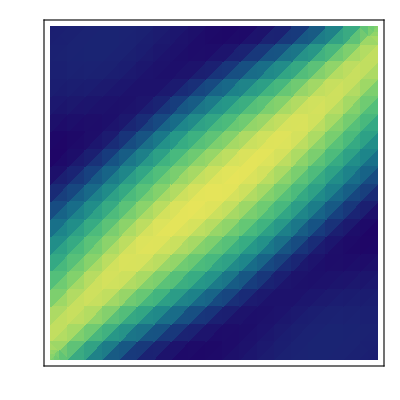

```mathematica
density21[200,210,10]
```

# Now we use this toy to fit the data approximately. Good plots are made with the density13 function

```mathematica
Manipulate[
Rasterize[DensityPlot[
(*1) Evaluate the transmission*)
ComplexExpand[Abs[t21/.Subscript[Ω, 32]->x/.Subscript[Ω, 31]->y]],

(*2) Plot in the specified range*)
{Subscript[δω, 32],-200,200},{Subscript[δω, 31],-200,200},PlotPoints->20,

(*3) Label and pretty stuff*)
PlotLabel->Style[Row@{"Ω_32=",x,", Ω_31=",y," MHz"},FontSize->20],
LabelStyle->{FontSize->20},
ColorFunction->"Ocean",
Frame->True,FrameLabel->{"δω_32/2π (MHz)","δω_31/2π (MHz)"},

(*4) Dynamic legend*)
PlotRange->{Automatic,Automatic,{-limit,limit}},
PlotLegends->BarLegend[{Automatic,{-limit,limit}},
LegendLabel->"Emission (arb units)"],
ColorFunctionScaling->True,
ColorFunction->(ColorData["Ocean"][Rescale[#,{-limit,limit}]]&),
PlotPoints->30
]],
(*5) Adjust contrast and limit*)
Style["Range",Bold,Medium],Row[{Control[{{limit,1,"Range"},0.0001,10,0.0001}]}(*,Control[{{lower,0.0001,"Lower Limit"},0,9,0.0001}]},*),Spacer[20]],Delimiter,Delimiter,Delimiter,
Style["Driving amplitudes",Bold,Medium],
{{x,10,"Ω_32"},0,1000,10},{{y,10,"Ω_31"},0,1000,10}
]
```

#### Now we attempt to perform fitting to the solutions obtained

```mathematica
density12[Ω32_,Ω31_]:=
((*PLOT SIMULATION FOR A GIVEN SET OF DRIVING POWERS*)

(*1) Prepare data to plot*)
toPlot = Simplify[ComplexExpand[Abs[t32/.Subscript[Ω, 32]->Ω32/.Subscript[Ω, 31]->Ω31]]];

(*2) Perform plotting of the data*)
Manipulate[
DensityPlot[toPlot,{Subscript[δω, 32],-500,500},{Subscript[δω, 31],-500,500},PlotPoints->20,
PlotLabel->Style[Row@{"Ω_21∝",Ω32,", Ω_31∝",Ω31},FontSize->20],
LabelStyle->{FontSize->12},
ColorFunction->"Ocean",
Frame->True,FrameLabel->{"δω_32 (MHz)","δω_31(MHz)"},
(*The color function bar manipulation, which prevents overload*)
PlotRange->{Automatic,Automatic,{-limit,limit}},
PlotLegends->BarLegend[{Automatic,{-limit,limit}}],
ColorFunctionScaling->False,
ColorFunction->(ColorData["Ocean"][Rescale[#,{-limit,limit}]]&),
PlotPoints->30],
{limit,0.1,100}
]
)
```

```mathematica
(* 4) Evaluating the component of the 1-3 transition *)
density21[Ω32_,Ω31_]:=
(
toPlot = Simplify[ComplexExpand[Abs[t21/.Subscript[Ω, 32]->Ω32/.Subscript[Ω, 31]->Ω31]]];
DensityPlot[toPlot,{Subscript[δω, 32],-200,200},{Subscript[δω, 31],-200,200},PlotPoints->20,PlotLegends->Automatic,PlotLabel->Style[Row@{"Ω_32∝",Ω32,", Ω_31∝",Ω31},FontSize->20],LabelStyle->{FontSize->20},ColorFunction->"Ocean",AxesLabel->{"δω_32","δω_31"}]
)


density12[290,32]

(*Table[density21[Ω32*100,Ω32*100/100],{Ω32,1,10}]
*)
(*Ω32=10
density21[Ω32,Ω32/100]


Ω32=Ω32*10
density21[Ω32,Ω32*1]
density21[Ω32,Ω32*10]
density21[Ω32,Ω32*20]
density21[Ω32,Ω32*30]
density21[Ω32,Ω32*40]
density21[Ω32,Ω32*50]
density21[Ω32,Ω32*60]*)
```

## NPL (2-3) power range from -60 to -30 MW (1-3) power range from -50 to -20

```mathematica
plot53File[MW_,NPL_]:=
(
(*name="f13_f23_53_MW(-45dBm)_NPL(-55dBm).txt";*)
fileToLoad=StringJoin[NotebookDirectory[],"Data/","f13_f23_53_MW(",ToString[MW],"dBm)_NPL(",ToString[NPL],"dBm).txt"];
fileContent = Import[fileToLoad,"Data"];
powerNPl = 10^(NPL/10)*10^6;powerMW=10^(MW/10)*10^6;
ListDensityPlot[fileContent,Mesh->All,PlotLabel->Style[Row@{"Ω_32∝",powerNPl,", Ω_31∝",powerMW},FontSize->20],LabelStyle->{FontSize->20}]
)

plot53File[-50,-60]
plot53File[-50,-50]
plot53File[-50,-40]
plot53File[-50,-30]
```

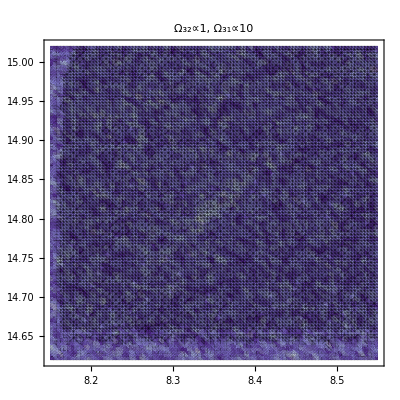

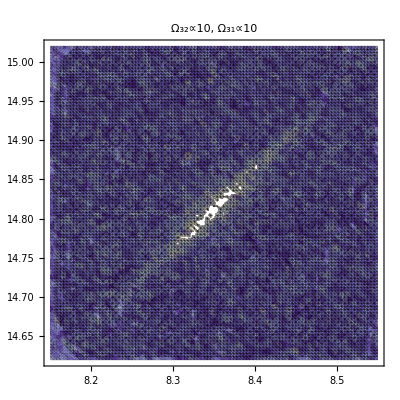

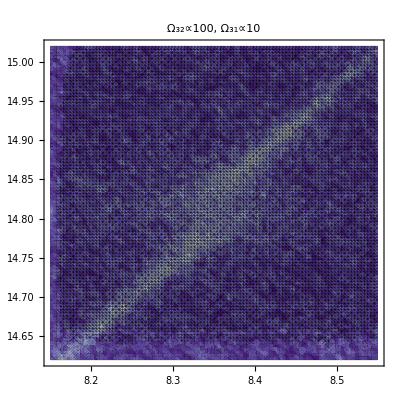

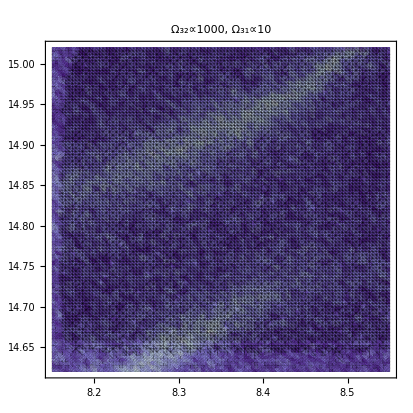

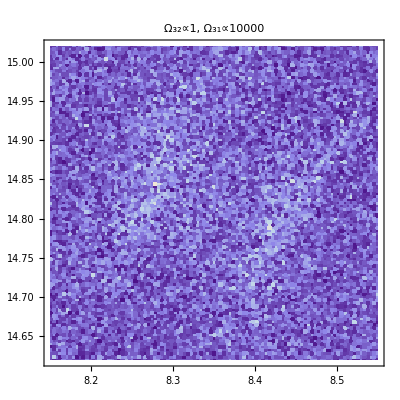

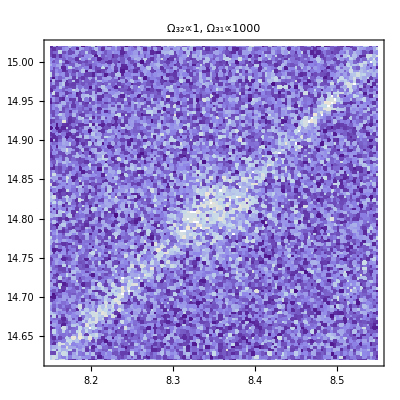

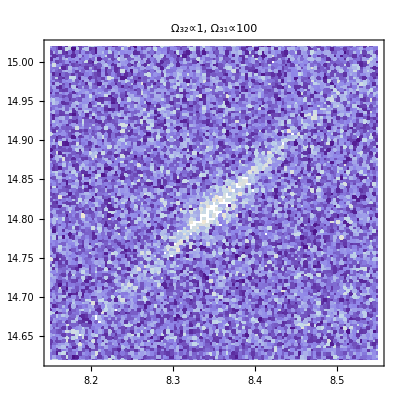

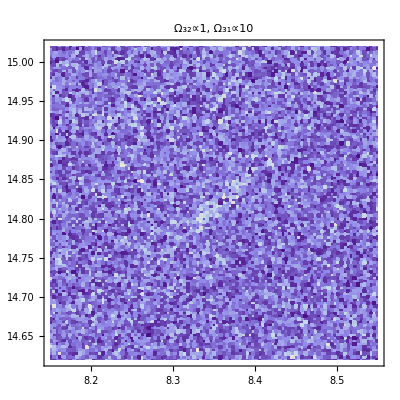

```mathematica
plotTest[MW_,NPL_]:=
(
(*name="f13_f23_53_MW(-45dBm)_NPL(-55dBm).txt";*)
fileToLoad=StringJoin[NotebookDirectory[],"Data/","f13_f23_53_MW(",ToString[MW],"dBm)_NPL(",ToString[NPL],"dBm).txt"];
fileContent = Import[fileToLoad,"Data"];
powerNPl = 10^(NPL/10)*10^6;powerMW=10^(MW/10)*10^6;
ListDensityPlot[fileContent,Mesh->None,InterpolationOrder->0,PlotLabel->Style[Row@{"Ω_32∝",powerNPl,", Ω_31∝",powerMW},FontSize->20],LabelStyle->{FontSize->20}]
)

plotTest[-20,-50]
plotTest[-30,-50]
plotTest[-40,-50]
plotTest[-50,-50]
```

```mathematica
Table[density21[10,10^(x/3)],{x,3,9}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}